Week 4: Rules and Patterns

```mathematica
(*Set evaluates the rule then applies it*)
n=1;
Expand[(a+1)^3] /. a->b^n++

NSolve[3x^2-7x+2-14x^7,x] (* Outputs a list of rules *)
Head[%[[1,1]]]

n
```

1+3 b+3 b^2+b^3

{{x→-0.832603-0.487531 ⅈ},{x→-0.832603+0.487531 ⅈ},{x→0.00902645-0.890067 ⅈ},{x→0.00902645+0.890067 ⅈ},{x→0.332087},{x→0.657533-0.388452 ⅈ},{x→0.657533+0.388452 ⅈ}}

Rule

2

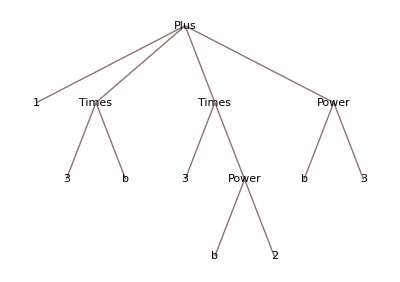

2

1+3 b+3 b^4+b^9

4

```mathematica
(* SetDelayed evaluates each time the rule is evaluated*)
n=1;
Expand[(a+1)^3]/.a->b^n++//TreeForm
n
n=1;
Expand[(a+1)^3] /. a:>b^n++
n
```

```mathematica
Clear[a];
n=1
a //. a:>a+1/n++^2 //N//FullForm
```

1

ReplaceRepeated::rrlim: Exiting after a scanned 65536 times.

Plus[1.64492,a]

```mathematica
Sum[1/n^2,{n,1,100000}] //N //FullForm
```

1.64492

```mathematica
N[Pi^2/6] //FullForm
```

1.64493

Patterns

```mathematica
n=1;
Expand[(x+y)^20];
Expand[(x+y)^20]//FullForm;
List@@Expand[(x+y)^20]//FullForm;
List@@Expand[(x+y)^20];
Cases[List @@Expand[(x+y)^20],__*x^_*y^_];
Cases[List @@Expand[(x+y)^20],__*x^m_*y^n_];
Cases[List @@Expand[(x+y)^20],__*x^m_*y^n_->{m,n}]
Cases[List @@Expand[(x+y)^20],__*x^m_*y^n_:>{m,n}]
Cases[List @@Expand[(x+y)^20],x^m_*y^n_:>{m,n}]
Cases[List @@Expand[(x+y)^20],n_Integer__:>n]
```

{{18,1},{17,1},{16,1},{15,1},{14,1},{13,1},{12,1},{11,1},{10,1},{9,1},{8,1},{7,1},{6,1},{5,1},{4,1},{3,1},{2,1}}

{{18,2},{17,3},{16,4},{15,5},{14,6},{13,7},{12,8},{11,9},{10,10},{9,11},{8,12},{7,13},{6,14},{5,15},{4,16},{3,17},{2,18}}

{}

{20,190,1140,4845,15504,38760,77520,125970,167960,184756,167960,125970,77520,38760,15504,4845,1140,190,20}

Patterns and Rules together

```mathematica
data=Import["http://www.basketball-reference.com/leagues/NBA_2014_games.html","Data"];
```

```mathematica
data[[2,2]];
played=Select[data[[2,2]],#[[2]]=="Box Score" &];
played[[All,3;;6]]

(* Team1Score - Team2Score *)
(* Need pairwise comparision getting a number and measurement is done a number of times *)
```

{{Orlando Magic,87,Indiana Pacers,97},{Los Angeles Clippers,103,Los Angeles Lakers,116},{Chicago Bulls,95,Miami Heat,107},{Brooklyn Nets,94,Cleveland Cavaliers,98},{Atlanta Hawks,109,Dallas Mavericks,118},{Washington Wizards,102,Detroit Pistons,113},{Los Angeles Lakers,94,Golden State Warriors,125},{Charlotte Bobcats,83,Houston Rockets,96},{Orlando Magic,115,Minnesota Timberwolves,120},{Indiana Pacers,95,New Orleans Pelicans,90},{Milwaukee Bucks,83,New York Knicks,90},{Miami Heat,110,Philadelphia 76ers,114},{Portland Trail Blazers,91,Phoenix Suns,104},{Denver Nuggets,88,Sacramento Kings,90},{Memphis Grizzlies,94,San Antonio Spurs,101},{Boston Celtics,87,Toronto Raptors,93},{Oklahoma City Thunder,101,Utah Jazz,98},{New York Knicks,81,Chicago Bulls,82},{Golden State Warriors,115,Los Angeles Clippers,126},{Toronto Raptors,95,Atlanta Hawks,102},{Milwaukee Bucks,105,Boston Celtics,98},{Miami Heat,100,Brooklyn Nets,101},{Cleveland Cavaliers,84,Charlotte Bobcats,90},{Portland Trail Blazers,113,Denver Nuggets,98},{Dallas Mavericks,105,Houston Rockets,113},{San Antonio Spurs,91,Los Angeles Lakers,85},{Detroit Pistons,108,Memphis Grizzlies,111},{Oklahoma City Thunder,81,Minnesota Timberwolves,100},{New Orleans Pelicans,90,Orlando Magic,110},{Utah Jazz,84,Phoenix Suns,87},{Los Angeles Clippers,110,Sacramento Kings,101},{Philadelphia 76ers,109,Washington Wizards,102},{Memphis Grizzlies,99,Dallas Mavericks,111},{Sacramento Kings,87,Golden State Warriors,98},{Cleveland Cavaliers,74,Indiana Pacers,89},{Toronto Raptors,97,Milwaukee Bucks,90},{Charlotte Bobcats,84,New Orleans Pelicans,105},{Chicago Bulls,104,Philadelphia 76ers,107},{San Antonio Spurs,105,Portland Trail Blazers,115},{Houston Rockets,104,Utah Jazz,93},{Boston Celtics,77,Detroit Pistons,87},{Atlanta Hawks,103,Los Angeles Lakers,105},{Washington Wizards,93,Miami Heat,103},{Minnesota Timberwolves,109,New York Knicks,100},{Phoenix Suns,96,Oklahoma City Thunder,103},{Brooklyn Nets,86,Orlando Magic,107},{Minnesota Timberwolves,92,Cleveland Cavaliers,93},{Houston Rockets,118,Los Angeles Clippers,137},{Boston Celtics,88,Memphis Grizzlies,95},{Golden State Warriors,110,Philadelphia 76ers,90},{Utah Jazz,88,Brooklyn Nets,104},{Los Angeles Lakers,104,Dallas Mavericks,123},{San Antonio Spurs,102,Denver Nuggets,94},{Indiana Pacers,99,Detroit Pistons,91},{Phoenix Suns,104,New Orleans Pelicans,98},{Charlotte Bobcats,102,New York Knicks,97},{Houston Rockets,116,Portland Trail Blazers,101},{Atlanta Hawks,105,Sacramento Kings,100},{Miami Heat,104,Toronto Raptors,95},{Utah Jazz,87,Boston Celtics,97},{Toronto Raptors,90,Charlotte Bobcats,92},{Chicago Bulls,80,Indiana Pacers,97},{New Orleans Pelicans,99,Memphis Grizzlies,84},{Cleveland Cavaliers,104,Milwaukee Bucks,109},{Golden State Warriors,106,Minnesota Timberwolves,93},{Dallas Mavericks,93,Oklahoma City Thunder,107},{Los Angeles Clippers,90,Orlando Magic,98},{Washington Wizards,116,Philadelphia 76ers,102},{Phoenix Suns,96,San Antonio Spurs,99},{Atlanta Hawks,107,Denver Nuggets,109},{Los Angeles Lakers,99,Houston Rockets,98},{Los Angeles Clippers,97,Miami Heat,102},{New York Knicks,101,Charlotte Bobcats,91},{Utah Jazz,73,Chicago Bulls,97},{Oklahoma City Thunder,119,Detroit Pistons,110},{Toronto Raptors,84,Indiana Pacers,91},{Dallas Mavericks,108,Minnesota Timberwolves,116},{Los Angeles Lakers,85,New Orleans Pelicans,96},{Boston Celtics,91,Orlando Magic,89},{Cleveland Cavaliers,79,Philadelphia 76ers,94},{Denver Nuggets,103,Phoenix Suns,114},{Sacramento Kings,91,Portland Trail Blazers,104},{Golden State Warriors,74,San Antonio Spurs,76},{Brooklyn Nets,108,Washington Wizards,112},{Orlando Magic,94,Atlanta Hawks,104},{Indiana Pacers,96,Brooklyn Nets,91},{Philadelphia 76ers,125,Cleveland Cavaliers,127},{Los Angeles Clippers,107,Houston Rockets,94},{Golden State Warriors,90,Memphis Grizzlies,108},{Boston Celtics,111,Miami Heat,110},{Dallas Mavericks,91,Milwaukee Bucks,83},{Portland Trail Blazers,96,Sacramento Kings,85},{Utah Jazz,91,Toronto Raptors,115},{Minnesota Timberwolves,113,Los Angeles Lakers,90},{San Antonio Spurs,120,New York Knicks,89},{Washington Wizards,105,Oklahoma City Thunder,106},{New Orleans Pelicans,94,Phoenix Suns,101},{Orlando Magic,105,Boston Celtics,120},{Atlanta Hawks,103,Charlotte Bobcats,94},{Cleveland Cavaliers,81,Chicago Bulls,96},{Toronto Raptors,104,Houston Rockets,110},{Memphis Grizzlies,79,Indiana Pacers,95},{Minnesota Timberwolves,107,Los Angeles Clippers,109},{San Antonio Spurs,109,Philadelphia 76ers,85},{Detroit Pistons,103,Portland Trail Blazers,109},{Denver Nuggets,100,Utah Jazz,81},{Washington Wizards,95,Dallas Mavericks,105},{Detroit Pistons,95,Golden State Warriors,113},{New Orleans Pelicans,95,Los Angeles Lakers,116},{Milwaukee Bucks,95,Miami Heat,118},{New York Knicks,95,Atlanta Hawks,91},{Charlotte Bobcats,89,Boston Celtics,83},{Los Angeles Lakers,99,Denver Nuggets,111},{Oklahoma City Thunder,103,Los Angeles Clippers,111},{Toronto Raptors,103,Memphis Grizzlies,87},{Cleveland Cavaliers,95,Minnesota Timberwolves,124},{Milwaukee Bucks,91,Orlando Magic,94},{Houston Rockets,117,Philadelphia 76ers,123},{Phoenix Suns,89,Portland Trail Blazers,90},{Brooklyn Nets,86,Sacramento Kings,107},{Washington Wizards,79,San Antonio Spurs,92},{New Orleans Pelicans,105,Utah Jazz,111},{Oklahoma City Thunder,115,Golden State Warriors,116},{Houston Rockets,109,New York Knicks,106},{Philadelphia 76ers,103,Atlanta Hawks,113},{Portland Trail Blazers,109,Boston Celtics,96},{Charlotte Bobcats,86,Cleveland Cavaliers,80},{Minnesota Timberwolves,113,Denver Nuggets,117},{Milwaukee Bucks,77,Indiana Pacers,104},{Memphis Grizzlies,89,Los Angeles Lakers,86},{Dallas Mavericks,104,Miami Heat,110},{Brooklyn Nets,100,Phoenix Suns,98},{Detroit Pistons,97,Sacramento Kings,90},{Chicago Bulls,96,Toronto Raptors,80},{San Antonio Spurs,91,Utah Jazz,82},{Miami Heat,97,Charlotte Bobcats,81},{Indiana Pacers,94,Chicago Bulls,110},{Utah Jazz,88,Golden State Warriors,102},{Denver Nuggets,111,Houston Rockets,122},{Brooklyn Nets,103,Los Angeles Clippers,110},{Oklahoma City Thunder,92,Milwaukee Bucks,79},{Boston Celtics,88,Minnesota Timberwolves,106},{Philadelphia 76ers,98,New Orleans Pelicans,135},{Atlanta Hawks,110,New York Knicks,90},{Dallas Mavericks,108,Orlando Magic,100},{Cleveland Cavaliers,103,Washington Wizards,96},{Detroit Pistons,99,Los Angeles Lakers,114},{Memphis Grizzlies,97,Sacramento Kings,86},{Portland Trail Blazers,118,Toronto Raptors,110},{Portland Trail Blazers,108,Brooklyn Nets,98},{Charlotte Bobcats,81,Chicago Bulls,86},{Philadelphia 76ers,94,Dallas Mavericks,97},{Memphis Grizzlies,106,Los Angeles Clippers,102},{Denver Nuggets,113,Oklahoma City Thunder,115},{Golden State Warriors,98,Utah Jazz,87},{New York Knicks,86,Detroit Pistons,92},{Boston Celtics,85,Houston Rockets,109},{Atlanta Hawks,88,Miami Heat,104},{Phoenix Suns,104,Sacramento Kings,107},{Minnesota Timberwolves,100,Washington Wizards,104},{Detroit Pistons,85,Atlanta Hawks,93},{Brooklyn Nets,91,Charlotte Bobcats,95},{Washington Wizards,98,Cleveland Cavaliers,91},{Houston Rockets,120,Dallas Mavericks,123},{Memphis Grizzlies,88,Golden State Warriors,81},{Portland Trail Blazers,91,Milwaukee Bucks,82},{Los Angeles Clippers,102,Minnesota Timberwolves,98},{Utah Jazz,98,New Orleans Pelicans,105},{Indiana Pacers,103,New York Knicks,96},{Miami Heat,120,Orlando Magic,92},{Toronto Raptors,108,Philadelphia 76ers,98},{Sacramento Kings,113,Phoenix Suns,106},{Boston Celtics,93,San Antonio Spurs,104},{Chicago Bulls,87,Denver Nuggets,97},{Los Angeles Clippers,91,Oklahoma City Thunder,105},{Indiana Pacers,97,Boston Celtics,82},{Phoenix Suns,98,Charlotte Bobcats,91},{Utah Jazz,93,Dallas Mavericks,103},{Atlanta Hawks,96,Detroit Pistons,89},{Golden State Warriors,95,Los Angeles Lakers,102},{San Antonio Spurs,102,Memphis Grizzlies,86},{Brooklyn Nets,81,Minnesota Timberwolves,111},{Cleveland Cavaliers,100,New Orleans Pelicans,104},{Milwaukee Bucks,107,Philadelphia 76ers,115},{Chicago Bulls,95,Portland Trail Blazers,98},{Washington Wizards,88,Toronto Raptors,96},{Boston Celtics,94,Atlanta Hawks,87},{Dallas Mavericks,100,Denver Nuggets,102},{Portland Trail Blazers,113,Golden State Warriors,101},{Minnesota Timberwolves,101,Houston Rockets,112},{Philadelphia 76ers,98,Indiana Pacers,106},{Sacramento Kings,102,Los Angeles Clippers,103},{Orlando Magic,99,Miami Heat,101},{Charlotte Bobcats,96,Milwaukee Bucks,72},{Cleveland Cavaliers,96,San Antonio Spurs,126},{New York Knicks,89,Washington Wizards,98},{Detroit Pistons,109,Brooklyn Nets,97},{Chicago Bulls,82,Los Angeles Clippers,121},{Sacramento Kings,86,Los Angeles Lakers,100},{Utah Jazz,73,Oklahoma City Thunder,95},{Phoenix Suns,104,Orlando Magic,96},{Boston Celtics,96,Charlotte Bobcats,86},{Denver Nuggets,110,Dallas Mavericks,96},{Milwaukee Bucks,94,Detroit Pistons,113},{Minnesota Timberwolves,84,Indiana Pacers,98},{Houston Rockets,93,Memphis Grizzlies,86},{Phoenix Suns,92,Miami Heat,107},{New York Knicks,91,Portland Trail Blazers,102},{New Orleans Pelicans,93,San Antonio Spurs,112},{Chicago Bulls,83,Utah Jazz,89},{Orlando Magic,109,Atlanta Hawks,92},{Golden State Warriors,102,New Orleans Pelicans,101},{Brooklyn Nets,102,Toronto Raptors,100},{Los Angeles Lakers,111,Washington Wizards,116},{Memphis Grizzlies,100,Boston Celtics,93},{Los Angeles Lakers,99,Brooklyn Nets,94},{Indiana Pacers,99,Charlotte Bobcats,74},{Miami Heat,95,Cleveland Cavaliers,84},{Golden State Warriors,99,Dallas Mavericks,103},{Chicago Bulls,99,Detroit Pistons,79},{Atlanta Hawks,84,Houston Rockets,113},{New York Knicks,80,Los Angeles Clippers,93},{Washington Wizards,100,Milwaukee Bucks,92},{Denver Nuggets,117,Minnesota Timberwolves,110},{San Antonio Spurs,88,Oklahoma City Thunder,94},{Philadelphia 76ers,94,Orlando Magic,105},{Portland Trail Blazers,106,Phoenix Suns,120},{Dallas Mavericks,87,Atlanta Hawks,88},{Cleveland Cavaliers,86,Boston Celtics,103},{Milwaukee Bucks,76,Charlotte Bobcats,92},{New York Knicks,95,Denver Nuggets,97},{Los Angeles Lakers,106,Detroit Pistons,102},{Brooklyn Nets,95,Houston Rockets,114},{Washington Wizards,73,Indiana Pacers,93},{Golden State Warriors,112,Oklahoma City Thunder,113},{San Antonio Spurs,109,Orlando Magic,91},{New Orleans Pelicans,121,Philadelphia 76ers,105},{Los Angeles Clippers,104,Sacramento Kings,98},{Miami Heat,90,Toronto Raptors,83},{Phoenix Suns,112,Utah Jazz,101},{Chicago Bulls,93,Cleveland Cavaliers,97},{Minnesota Timberwolves,112,Dallas Mavericks,106},{Brooklyn Nets,97,Memphis Grizzlies,88},{Boston Celtics,85,Milwaukee Bucks,92},{Utah Jazz,112,Phoenix Suns,104},{Houston Rockets,112,San Antonio Spurs,106},{Atlanta Hawks,101,Washington Wizards,108},{Philadelphia 76ers,100,Detroit Pistons,115},{Indiana Pacers,105,Los Angeles Clippers,100},{Portland Trail Blazers,114,Los Angeles Lakers,108},{Charlotte Bobcats,98,Miami Heat,99},{New Orleans Pelicans,103,New York Knicks,99},{Minnesota Timberwolves,103,Oklahoma City Thunder,113},{Golden State Warriors,115,Sacramento Kings,113},{Denver Nuggets,112,Toronto Raptors,98},{New Orleans Pelicans,131,Chicago Bulls,128},{Indiana Pacers,102,Portland Trail Blazers,106},{Atlanta Hawks,100,San Antonio Spurs,102},{Houston Rockets,103,Utah Jazz,109},{Orlando Magic,80,Washington Wizards,98},{Milwaukee Bucks,100,Boston Celtics,108},{Denver Nuggets,111,Brooklyn Nets,87},{Charlotte Bobcats,82,Dallas Mavericks,89},{Toronto Raptors,103,Golden State Warriors,112},{Phoenix Suns,91,Memphis Grizzlies,110},{Detroit Pistons,107,Miami Heat,97},{Orlando Magic,125,Philadelphia 76ers,126},{Oklahoma City Thunder,97,Sacramento Kings,95},{Los Angeles Clippers,97,Atlanta Hawks,107},{Denver Nuggets,88,Cleveland Cavaliers,98},{Phoenix Suns,97,Houston Rockets,88},{Detroit Pistons,105,Milwaukee Bucks,98},{Dallas Mavericks,100,New Orleans Pelicans,97},{Oklahoma City Thunder,104,Portland Trail Blazers,111},{Indiana Pacers,95,Utah Jazz,86},{New York Knicks,113,Brooklyn Nets,83},{Miami Heat,87,Chicago Bulls,107},{Los Angeles Clippers,101,Memphis Grizzlies,81},{Cleveland Cavaliers,89,Atlanta Hawks,108},{Denver Nuggets,98,Boston Celtics,106},{Philadelphia 76ers,88,Charlotte Bobcats,105},{Golden State Warriors,83,Houston Rockets,105},{Oklahoma City Thunder,109,New Orleans Pelicans,95},{Orlando Magic,83,New York Knicks,121},{Toronto Raptors,97,Phoenix Suns,106},{Utah Jazz,98,Portland Trail Blazers,130},{Los Angeles Lakers,106,Sacramento Kings,100},{Milwaukee Bucks,109,Washington Wizards,105},{Detroit Pistons,92,Chicago Bulls,75},{Los Angeles Clippers,82,Cleveland Cavaliers,88},{Golden State Warriors,108,Memphis Grizzlies,82},{Brooklyn Nets,90,Milwaukee Bucks,82},{Miami Heat,103,Minnesota Timberwolves,82},{Denver Nuggets,103,Philadelphia 76ers,92},{Dallas Mavericks,108,Portland Trail Blazers,106},{Indiana Pacers,111,San Antonio Spurs,100},{Sacramento Kings,112,Utah Jazz,102},{Miami Heat,110,Detroit Pistons,95},{Orlando Magic,88,Houston Rockets,98},{Toronto Raptors,106,Los Angeles Lakers,94},{Boston Celtics,114,New York Knicks,73},{Indiana Pacers,94,Oklahoma City Thunder,118},{Golden State Warriors,111,Charlotte Bobcats,115},{Orlando Magic,85,Memphis Grizzlies,94},{Los Angeles Clippers,94,Philadelphia 76ers,83},{Dallas Mavericks,97,Sacramento Kings,112},{Portland Trail Blazers,105,Utah Jazz,94},{Denver Nuggets,75,Washington Wizards,74},{Oklahoma City Thunder,101,Atlanta Hawks,92},{Boston Celtics,96,Brooklyn Nets,104},{Milwaukee Bucks,78,Chicago Bulls,74},{New York Knicks,94,Cleveland Cavaliers,109},{Minnesota Timberwolves,121,Detroit Pistons,94},{Miami Heat,84,Indiana Pacers,90},{Phoenix Suns,114,Los Angeles Lakers,108},{San Antonio Spurs,116,Toronto Raptors,103},{Los Angeles Clippers,96,Boston Celtics,88},{Orlando Magic,92,Charlotte Bobcats,83},{Dallas Mavericks,93,Golden State Warriors,95},{Oklahoma City Thunder,116,Memphis Grizzlies,100},{San Antonio Spurs,109,Milwaukee Bucks,77},{Philadelphia 76ers,99,Minnesota Timberwolves,106},{Detroit Pistons,106,New Orleans Pelicans,111},{Chicago Bulls,78,New York Knicks,83},{Utah Jazz,122,Sacramento Kings,101},{Los Angeles Clippers,93,Brooklyn Nets,102},{Houston Rockets,104,Portland Trail Blazers,111},{Washington Wizards,99,Atlanta Hawks,101},{New York Knicks,86,Boston Celtics,90},{Utah Jazz,103,Denver Nuggets,93},{Brooklyn Nets,99,Detroit Pistons,103},{Houston Rockets,116,Golden State Warriors,112},{Charlotte Bobcats,94,Indiana Pacers,99},{Chicago Bulls,91,Milwaukee Bucks,90},{Memphis Grizzlies,98,New Orleans Pelicans,104},{Los Angeles Lakers,97,Oklahoma City Thunder,122},{Cleveland Cavaliers,109,Orlando Magic,100},{Sacramento Kings,107,Phoenix Suns,116},{Minnesota Timberwolves,110,San Antonio Spurs,117},{Philadelphia 76ers,100,Toronto Raptors,108},{Los Angeles Lakers,88,Charlotte Bobcats,85},{Toronto Raptors,99,Chicago Bulls,77},{Milwaukee Bucks,93,Dallas Mavericks,106},{Cleveland Cavaliers,107,Miami Heat,114},{Atlanta Hawks,106,New York Knicks,111},{Portland Trail Blazers,139,Philadelphia 76ers,105},{San Antonio Spurs,100,Utah Jazz,84},{Los Angeles Clippers,113,Washington Wizards,97},{New Orleans Pelicans,93,Denver Nuggets,102},{Portland Trail Blazers,111,Detroit Pistons,109},{Minnesota Timberwolves,101,Memphis Grizzlies,93},{Orlando Magic,98,Oklahoma City Thunder,101},{Golden State Warriors,102,Phoenix Suns,106},{Houston Rockets,91,Sacramento Kings,106},{Los Angeles Lakers,100,Atlanta Hawks,114},{Minnesota Timberwolves,97,Boston Celtics,101},{Philadelphia 76ers,94,Brooklyn Nets,130},{Orlando Magic,83,Chicago Bulls,82},{Detroit Pistons,101,Indiana Pacers,96},{San Antonio Spurs,92,Los Angeles Clippers,115},{Utah Jazz,94,Miami Heat,117},{Washington Wizards,102,New York Knicks,101},{Sacramento Kings,87,Charlotte Bobcats,95},{Portland Trail Blazers,119,Cleveland Cavaliers,116},{Oklahoma City Thunder,105,Denver Nuggets,93},{New Orleans Pelicans,93,Golden State Warriors,104},{Los Angeles Lakers,96,Memphis Grizzlies,92},{Sacramento Kings,107,Atlanta Hawks,124},{Detroit Pistons,107,Boston Celtics,106},{Washington Wizards,113,Brooklyn Nets,107},{Memphis Grizzlies,91,Dallas Mavericks,105},{Chicago Bulls,94,Houston Rockets,109},{New Orleans Pelicans,95,Los Angeles Clippers,108},{Indiana Pacers,94,Miami Heat,97},{New York Knicks,107,Milwaukee Bucks,101},{Portland Trail Blazers,109,Minnesota Timberwolves,120},{Utah Jazz,86,Orlando Magic,82},{San Antonio Spurs,108,Phoenix Suns,101},{Charlotte Bobcats,104,Toronto Raptors,102},{San Antonio Spurs,104,Golden State Warriors,102},{Chicago Bulls,95,Oklahoma City Thunder,107},{Utah Jazz,85,Atlanta Hawks,118},{Milwaukee Bucks,111,Cleveland Cavaliers,114},{Toronto Raptors,109,Dallas Mavericks,108},{Phoenix Suns,103,Denver Nuggets,99},{Charlotte Bobcats,116,Detroit Pistons,106},{Houston Rockets,81,Indiana Pacers,114},{Minnesota Timberwolves,91,Los Angeles Lakers,104},{Sacramento Kings,103,Miami Heat,122},{Brooklyn Nets,120,Philadelphia 76ers,121},{Washington Wizards,106,Boston Celtics,99},{Utah Jazz,88,Charlotte Bobcats,85},{Cleveland Cavaliers,84,Chicago Bulls,100},{Houston Rockets,114,Detroit Pistons,97},{Los Angeles Lakers,83,Golden State Warriors,102},{Denver Nuggets,91,Los Angeles Clippers,112},{Philadelphia 76ers,106,Milwaukee Bucks,116},{Memphis Grizzlies,95,New York Knicks,87},{Sacramento Kings,105,Orlando Magic,100},{Dallas Mavericks,108,Phoenix Suns,123},{New Orleans Pelicans,107,Portland Trail Blazers,110},{Oklahoma City Thunder,113,San Antonio Spurs,100},{Boston Celtics,79,Indiana Pacers,106},{Minnesota Timberwolves,116,Los Angeles Clippers,120},{Toronto Raptors,104,Oklahoma City Thunder,98},{Indiana Pacers,103,Brooklyn Nets,86},{Milwaukee Bucks,110,Charlotte Bobcats,111},{Detroit Pistons,115,Cleveland Cavaliers,92},{Golden State Warriors,89,Denver Nuggets,81},{Dallas Mavericks,111,Houston Rockets,104},{Utah Jazz,94,Memphis Grizzlies,104},{Atlanta Hawks,119,Miami Heat,121},{New York Knicks,103,Orlando Magic,98},{Los Angeles Lakers,90,Phoenix Suns,117},{New Orleans Pelicans,113,Sacramento Kings,100},{Toronto Raptors,99,San Antonio Spurs,112},{Chicago Bulls,95,Brooklyn Nets,78},{Los Angeles Clippers,103,Golden State Warriors,105},{Miami Heat,101,Los Angeles Lakers,95},{Oklahoma City Thunder,123,New York Knicks,94},{Houston Rockets,111,San Antonio Spurs,98},{Atlanta Hawks,127,Cleveland Cavaliers,125},{San Antonio Spurs,116,Dallas Mavericks,107},{Memphis Grizzlies,92,Houston Rockets,100},{Los Angeles Clippers,112,Portland Trail Blazers,116},{Milwaukee Bucks,93,Brooklyn Nets,104},{Oklahoma City Thunder,89,Charlotte Bobcats,85},{Phoenix Suns,86,Golden State Warriors,115},{Washington Wizards,98,Minnesota Timberwolves,120},{Denver Nuggets,89,New Orleans Pelicans,105},{Toronto Raptors,95,New York Knicks,83},{Detroit Pistons,92,Orlando Magic,109},{Miami Heat,103,Sacramento Kings,108},{Los Angeles Lakers,103,Utah Jazz,105},{Charlotte Bobcats,116,Atlanta Hawks,118},{Cleveland Cavaliers,100,Boston Celtics,103},{Dallas Mavericks,105,Chicago Bulls,83},{New Orleans Pelicans,98,Houston Rockets,107},{Brooklyn Nets,91,Indiana Pacers,105},{Utah Jazz,90,Los Angeles Clippers,98},{Denver Nuggets,99,Memphis Grizzlies,120},{Minnesota Timberwolves,117,Milwaukee Bucks,95},{Philadelphia 76ers,101,Phoenix Suns,115},{Miami Heat,108,Portland Trail Blazers,107},{New York Knicks,100,Toronto Raptors,115},{Detroit Pistons,82,Washington Wizards,106},{Golden State Warriors,108,Cleveland Cavaliers,104},{Philadelphia 76ers,111,Los Angeles Lakers,104},{Houston Rockets,86,Oklahoma City Thunder,117},{Atlanta Hawks,102,Orlando Magic,109},{Sacramento Kings,104,San Antonio Spurs,112},{Miami Heat,97,Denver Nuggets,94},{Washington Wizards,106,Detroit Pistons,99},{Phoenix Suns,107,Los Angeles Clippers,88},{Chicago Bulls,95,Memphis Grizzlies,91},{Dallas Mavericks,100,Minnesota Timberwolves,98},{Portland Trail Blazers,108,New Orleans Pelicans,110},{Charlotte Bobcats,80,Utah Jazz,83},{Atlanta Hawks,92,Boston Celtics,91},{Toronto Raptors,85,Chicago Bulls,79},{Sacramento Kings,110,Houston Rockets,106},{Cleveland Cavaliers,76,Indiana Pacers,91},{Milwaukee Bucks,94,Los Angeles Lakers,79},{Portland Trail Blazers,98,Oklahoma City Thunder,94},{Golden State Warriors,94,Orlando Magic,81},{Brooklyn Nets,92,San Antonio Spurs,113},{Philadelphia 76ers,114,Denver Nuggets,102},{Charlotte Bobcats,85,Los Angeles Clippers,112},{New Orleans Pelicans,112,Minnesota Timberwolves,124},{Indiana Pacers,82,Toronto Raptors,95},{Dallas Mavericks,87,Washington Wizards,78},{Boston Celtics,82,Chicago Bulls,94},{Orlando Magic,81,Cleveland Cavaliers,87},{Golden State Warriors,123,Miami Heat,114},{Brooklyn Nets,95,Oklahoma City Thunder,93},{Memphis Grizzlies,99,Phoenix Suns,91},{Charlotte Bobcats,104,Portland Trail Blazers,134},{Philadelphia 76ers,113,Sacramento Kings,104},{New York Knicks,105,San Antonio Spurs,101},{Milwaukee Bucks,87,Utah Jazz,96},{Golden State Warriors,101,Atlanta Hawks,100},{New Orleans Pelicans,95,Boston Celtics,92},{Los Angeles Clippers,119,Dallas Mavericks,112},{Memphis Grizzlies,108,Denver Nuggets,111},{New York Knicks,100,Houston Rockets,102},{Utah Jazz,99,Los Angeles Lakers,110},{Toronto Raptors,101,Washington Wizards,88},{Cleveland Cavaliers,82,Brooklyn Nets,89},{Atlanta Hawks,84,Chicago Bulls,91},{New Orleans Pelicans,82,Indiana Pacers,99},{Oklahoma City Thunder,115,Minnesota Timberwolves,111},{Miami Heat,110,Orlando Magic,94},{Milwaukee Bucks,100,Phoenix Suns,116},{Philadelphia 76ers,101,Portland Trail Blazers,99},{Charlotte Bobcats,113,Sacramento Kings,103},{Los Angeles Clippers,92,San Antonio Spurs,116},{Indiana Pacers,82,Cleveland Cavaliers,78},{New York Knicks,92,Dallas Mavericks,80},{Memphis Grizzlies,112,Detroit Pistons,84},{Denver Nuggets,137,Los Angeles Lakers,115},{Toronto Raptors,97,Miami Heat,102},{Boston Celtics,96,Oklahoma City Thunder,119},{Golden State Warriors,112,Washington Wizards,96},{Atlanta Hawks,86,Brooklyn Nets,91},{Orlando Magic,81,Los Angeles Clippers,101},{Minnesota Timberwolves,126,Philadelphia 76ers,95},{Washington Wizards,97,Charlotte Bobcats,83},{Phoenix Suns,87,Chicago Bulls,92},{Philadelphia 76ers,93,Cleveland Cavaliers,111},{Los Angeles Lakers,97,Dallas Mavericks,110},{Boston Celtics,98,Denver Nuggets,129},{Toronto Raptors,79,Indiana Pacers,86},{San Antonio Spurs,110,Memphis Grizzlies,108},{New Orleans Pelicans,88,Miami Heat,107},{Golden State Warriors,101,Milwaukee Bucks,80},{Detroit Pistons,85,New York Knicks,89},{Portland Trail Blazers,119,Sacramento Kings,123},{Oklahoma City Thunder,101,Utah Jazz,112},{Indiana Pacers,87,Atlanta Hawks,97},{Golden State Warriors,98,Brooklyn Nets,102},{Los Angeles Lakers,99,Houston Rockets,113},{Boston Celtics,105,Los Angeles Clippers,111},{Phoenix Suns,104,Minnesota Timberwolves,103},{Washington Wizards,102,New Orleans Pelicans,96},{Orlando Magic,94,Portland Trail Blazers,110},{Dallas Mavericks,90,San Antonio Spurs,112},{Detroit Pistons,91,Toronto Raptors,112},{Oklahoma City Thunder,88,Denver Nuggets,101},{Miami Heat,92,New York Knicks,102},{Houston Rockets,80,Atlanta Hawks,83},{Miami Heat,95,Brooklyn Nets,104},{Boston Celtics,97,Golden State Warriors,99},{Washington Wizards,66,Indiana Pacers,93},{Los Angeles Lakers,87,Los Angeles Clippers,123},{Phoenix Suns,99,Memphis Grizzlies,104},{Chicago Bulls,81,Milwaukee Bucks,72},{Charlotte Bobcats,92,Minnesota Timberwolves,119},{Dallas Mavericks,107,New Orleans Pelicans,90},{Detroit Pistons,114,Philadelphia 76ers,104},{Orlando Magic,83,Sacramento Kings,103},{Cleveland Cavaliers,113,Utah Jazz,102},{Charlotte Bobcats,97,Chicago Bulls,103},{New Orleans Pelicans,107,Dallas Mavericks,110},{Orlando Magic,94,Denver Nuggets,120},{Phoenix Suns,108,Detroit Pistons,110},{Milwaukee Bucks,85,Oklahoma City Thunder,101},{New York Knicks,102,Philadelphia 76ers,92},{Boston Celtics,104,Portland Trail Blazers,112},{Brooklyn Nets,80,Toronto Raptors,96},{Houston Rockets,114,Washington Wizards,107},{Atlanta Hawks,101,Memphis Grizzlies,108},{Cleveland Cavaliers,80,Sacramento Kings,124},{Minnesota Timberwolves,86,San Antonio Spurs,104},{Houston Rockets,104,Boston Celtics,92},{Washington Wizards,102,Chicago Bulls,88},{Orlando Magic,88,Dallas Mavericks,107},{San Antonio Spurs,101,New Orleans Pelicans,95},{Phoenix Suns,96,New York Knicks,98},{Milwaukee Bucks,94,Toronto Raptors,116},{Denver Nuggets,103,Utah Jazz,118},{New York Knicks,98,Charlotte Bobcats,108},{Sacramento Kings,92,Indiana Pacers,116},{Cleveland Cavaliers,120,Los Angeles Lakers,118},{Oklahoma City Thunder,87,Memphis Grizzlies,90},{Toronto Raptors,83,Boston Celtics,88},{Denver Nuggets,123,Golden State Warriors,116},{Dallas Mavericks,127,Los Angeles Clippers,129},{Memphis Grizzlies,82,Milwaukee Bucks,77},{Sacramento Kings,111,Minnesota Timberwolves,108},{Houston Rockets,103,New Orleans Pelicans,100},{Chicago Bulls,128,Orlando Magic,125},{Charlotte Bobcats,92,Philadelphia 76ers,95},{Los Angeles Lakers,114,Phoenix Suns,121},{Cleveland Cavaliers,96,Portland Trail Blazers,108},{Utah Jazz,105,San Antonio Spurs,109},{Miami Heat,97,Washington Wizards,114},{Brooklyn Nets,127,Atlanta Hawks,110},{Oklahoma City Thunder,104,Houston Rockets,92},{New York Knicks,89,Indiana Pacers,117},{Los Angeles Lakers,107,Boston Celtics,104},{Cleveland Cavaliers,117,Denver Nuggets,109},{Utah Jazz,110,Detroit Pistons,89},{Sacramento Kings,90,Memphis Grizzlies,91},{Los Angeles Clippers,109,New York Knicks,95},{Golden State Warriors,121,Oklahoma City Thunder,127},{Charlotte Bobcats,111,Orlando Magic,101},{Miami Heat,101,Philadelphia 76ers,86},{Dallas Mavericks,110,Phoenix Suns,107},{Portland Trail Blazers,109,San Antonio Spurs,100},{Minnesota Timberwolves,89,Toronto Raptors,94},{Chicago Bulls,93,Washington Wizards,96},{Miami Heat,104,Charlotte Bobcats,96},{Philadelphia 76ers,78,Chicago Bulls,103},{Portland Trail Blazers,127,Dallas Mavericks,111},{Milwaukee Bucks,104,Houston Rockets,114},{Los Angeles Clippers,92,Indiana Pacers,106},{Utah Jazz,72,Minnesota Timberwolves,98},{Golden State Warriors,97,New Orleans Pelicans,87},{Detroit Pistons,104,Washington Wizards,98},{Sacramento Kings,93,Oklahoma City Thunder,108},{Boston Celtics,91,Orlando Magic,93},{Denver Nuggets,103,Phoenix Suns,117},{Milwaukee Bucks,82,San Antonio Spurs,110},{Los Angeles Lakers,112,Toronto Raptors,106},{Miami Heat,114,Atlanta Hawks,121},{Toronto Raptors,95,Charlotte Bobcats,100},{Los Angeles Lakers,100,Chicago Bulls,102},{Dallas Mavericks,102,Cleveland Cavaliers,97},{Los Angeles Clippers,112,Detroit Pistons,103},{Indiana Pacers,102,Golden State Warriors,94},{Portland Trail Blazers,113,Houston Rockets,126},{New Orleans Pelicans,95,Memphis Grizzlies,92},{Brooklyn Nets,103,New York Knicks,80},{Philadelphia 76ers,99,Washington Wizards,107},{Orlando Magic,90,Brooklyn Nets,101},{Boston Celtics,86,Miami Heat,93},{Sacramento Kings,114,New Orleans Pelicans,97},{Portland Trail Blazers,97,Oklahoma City Thunder,105},{Minnesota Timberwolves,112,Utah Jazz,97},{Los Angeles Clippers,91,Charlotte Bobcats,95},{Chicago Bulls,98,Cleveland Cavaliers,87},{Sacramento Kings,98,Houston Rockets,119},{Detroit Pistons,101,Milwaukee Bucks,104},{Philadelphia 76ers,110,New York Knicks,106},{Atlanta Hawks,112,Orlando Magic,109},{Indiana Pacers,100,Phoenix Suns,124},{Oklahoma City Thunder,111,San Antonio Spurs,105},{Dallas Mavericks,85,Toronto Raptors,93},{Boston Celtics,113,Washington Wizards,111},{Los Angeles Lakers,102,Miami Heat,109},{Denver Nuggets,105,Portland Trail Blazers,110},{San Antonio Spurs,105,Atlanta Hawks,79},{Oklahoma City Thunder,101,Boston Celtics,83},{Dallas Mavericks,106,Brooklyn Nets,107},{Los Angeles Clippers,112,Chicago Bulls,95},{Milwaukee Bucks,78,Cleveland Cavaliers,93},{New Orleans Pelicans,103,Detroit Pistons,101},{Minnesota Timberwolves,121,Golden State Warriors,120},{Memphis Grizzlies,88,Houston Rockets,87},{Charlotte Bobcats,96,New York Knicks,125},{Los Angeles Lakers,105,Orlando Magic,114},{Toronto Raptors,104,Philadelphia 76ers,95},{Washington Wizards,101,Phoenix Suns,95},{Indiana Pacers,116,Sacramento Kings,111},{Chicago Bulls,89,Charlotte Bobcats,87},{Indiana Pacers,96,Denver Nuggets,109},{Houston Rockets,81,Memphis Grizzlies,99},{Atlanta Hawks,112,Milwaukee Bucks,87},{Oklahoma City Thunder,103,Philadelphia 76ers,91},{Minnesota Timberwolves,104,Portland Trail Blazers,115},{Los Angeles Clippers,126,Toronto Raptors,118},{Washington Wizards,101,Utah Jazz,104},{Brooklyn Nets,85,Boston Celtics,79},{Phoenix Suns,99,Cleveland Cavaliers,90},{Detroit Pistons,106,Dallas Mavericks,116},{Portland Trail Blazers,88,Golden State Warriors,103},{San Antonio Spurs,101,Miami Heat,113},{Orlando Magic,92,New Orleans Pelicans,100},{Los Angeles Lakers,103,New York Knicks,110},{Denver Nuggets,125,Sacramento Kings,117},{Toronto Raptors,104,Brooklyn Nets,103},{Minnesota Timberwolves,95,Chicago Bulls,86},{Los Angeles Clippers,114,Milwaukee Bucks,86},{Atlanta Hawks,109,Oklahoma City Thunder,111},{Phoenix Suns,124,Philadelphia 76ers,113},{Sacramento Kings,99,Utah Jazz,106},{New Orleans Pelicans,100,Cleveland Cavaliers,89},{Orlando Magic,87,Detroit Pistons,103},{Washington Wizards,88,Golden State Warriors,85},{San Antonio Spurs,90,Houston Rockets,97},{Indiana Pacers,104,Los Angeles Lakers,92},{Boston Celtics,88,New York Knicks,114},{Memphis Grizzlies,98,Portland Trail Blazers,81},{Philadelphia 76ers,95,Boston Celtics,94},{Houston Rockets,117,Dallas Mavericks,115},{Charlotte Bobcats,101,Denver Nuggets,98},{Washington Wizards,103,Los Angeles Clippers,110},{Oklahoma City Thunder,112,Miami Heat,95},{Phoenix Suns,126,Milwaukee Bucks,117},{New Orleans Pelicans,77,Minnesota Timberwolves,88},{Memphis Grizzlies,99,Sacramento Kings,89},{Chicago Bulls,96,San Antonio Spurs,86},{Orlando Magic,83,Toronto Raptors,98},{Los Angeles Clippers,92,Golden State Warriors,111},{Phoenix Suns,102,Indiana Pacers,94},{Cleveland Cavaliers,86,New York Knicks,117},{Oklahoma City Thunder,120,Brooklyn Nets,95},{Sacramento Kings,103,Dallas Mavericks,107},{Toronto Raptors,100,Denver Nuggets,90},{Charlotte Bobcats,110,Los Angeles Lakers,100},{Memphis Grizzlies,94,Minnesota Timberwolves,90},{Milwaukee Bucks,102,Orlando Magic,113},{Atlanta Hawks,125,Philadelphia 76ers,99},{Golden State Warriors,95,Utah Jazz,90},{Minnesota Timberwolves,113,Atlanta Hawks,120},{Philadelphia 76ers,96,Detroit Pistons,113},{Cleveland Cavaliers,92,Houston Rockets,106},{Brooklyn Nets,96,Indiana Pacers,97},{Utah Jazz,87,Los Angeles Clippers,102},{Milwaukee Bucks,90,Memphis Grizzlies,99},{Chicago Bulls,79,New Orleans Pelicans,88},{Miami Heat,106,New York Knicks,91},{Charlotte Bobcats,95,Phoenix Suns,105},{Toronto Raptors,103,Portland Trail Blazers,106},{Sacramento Kings,93,San Antonio Spurs,95},{Oklahoma City Thunder,81,Washington Wizards,96},{Orlando Magic,89,Boston Celtics,96},{Philadelphia 76ers,102,Brooklyn Nets,108},{Cleveland Cavaliers,107,Dallas Mavericks,124},{Los Angeles Clippers,115,Denver Nuggets,116},{Orlando Magic,79,Indiana Pacers,98},{Detroit Pistons,96,Miami Heat,102},{New York Knicks,98,Milwaukee Bucks,101},{San Antonio Spurs,102,New Orleans Pelicans,95},{Memphis Grizzlies,77,Oklahoma City Thunder,86},{Chicago Bulls,70,Sacramento Kings,99},{Toronto Raptors,94,Utah Jazz,79},{Portland Trail Blazers,90,Washington Wizards,100},{Indiana Pacers,89,Atlanta Hawks,85},{Charlotte Bobcats,91,Golden State Warriors,75},{Los Angeles Lakers,99,Minnesota Timberwolves,109},{Chicago Bulls,101,Phoenix Suns,92},{Los Angeles Lakers,119,Cleveland Cavaliers,108},{Milwaukee Bucks,100,Denver Nuggets,110},{Phoenix Suns,108,Houston Rockets,122},{Miami Heat,116,Los Angeles Clippers,112},{Dallas Mavericks,110,Memphis Grizzlies,96},{Atlanta Hawks,100,New Orleans Pelicans,105},{Portland Trail Blazers,94,New York Knicks,90},{Minnesota Timberwolves,97,Oklahoma City Thunder,106},{Detroit Pistons,98,Orlando Magic,112},{Boston Celtics,114,Philadelphia 76ers,108},{Toronto Raptors,101,Sacramento Kings,109},{San Antonio Spurs,125,Washington Wizards,118},{San Antonio Spurs,89,Brooklyn Nets,103},{Chicago Bulls,87,Golden State Warriors,102},{Sacramento Kings,89,Boston Celtics,99},{Utah Jazz,81,Dallas Mavericks,103},{Brooklyn Nets,95,Detroit Pistons,111},{Portland Trail Blazers,113,Indiana Pacers,118},{Toronto Raptors,105,Los Angeles Clippers,118},{Minnesota Timberwolves,91,New Orleans Pelicans,98},{Denver Nuggets,90,New York Knicks,117},{Oklahoma City Thunder,102,Orlando Magic,103},{Los Angeles Lakers,112,Philadelphia 76ers,98},{Cleveland Cavaliers,115,Washington Wizards,113},{Memphis Grizzlies,79,Atlanta Hawks,76},{San Antonio Spurs,104,Charlotte Bobcats,100},{Denver Nuggets,109,Detroit Pistons,126},{Houston Rockets,101,Milwaukee Bucks,95},{Portland Trail Blazers,117,Minnesota Timberwolves,110},{Golden State Warriors,109,Phoenix Suns,122},{Miami Heat,89,Utah Jazz,94},{Dallas Mavericks,102,Boston Celtics,91},{New Orleans Pelicans,81,Brooklyn Nets,93},{Memphis Grizzlies,83,Cleveland Cavaliers,91},{Philadelphia 76ers,78,Los Angeles Clippers,123},{Chicago Bulls,92,Los Angeles Lakers,86},{New York Knicks,100,Oklahoma City Thunder,112},{Indiana Pacers,92,Orlando Magic,93},{Sacramento Kings,84,Washington Wizards,93},{San Antonio Spurs,100,Detroit Pistons,109},{Philadelphia 76ers,80,Golden State Warriors,123},{Denver Nuggets,80,Indiana Pacers,119},{Boston Celtics,102,Milwaukee Bucks,86},{Houston Rockets,107,Minnesota Timberwolves,89},{New Orleans Pelicans,101,Toronto Raptors,108}}

```mathematica
delta=played[[All,3;;6]]/. {_,n_,_,m_}:>n-m
```

{-10,-13,-12,-4,-9,-11,-31,-13,-5,5,-7,-4,-13,-2,-7,-6,3,-1,-11,-7,7,-1,-6,15,-8,6,-3,-19,-20,-3,9,7,-12,-11,-15,7,-21,-3,-10,11,-10,-2,-10,9,-7,-21,-1,-19,-7,20,-16,-19,8,8,6,5,15,5,9,-10,-2,-17,15,-5,13,-14,-8,14,-3,-2,1,-5,10,-24,9,-7,-8,-11,2,-15,-11,-13,-2,-4,-10,5,-2,13,-18,1,8,11,-24,23,31,-1,-7,-15,9,-15,-6,-16,-2,24,-6,19,-10,-18,-21,-23,4,6,-12,-8,16,-29,-3,-6,-1,-21,-13,-6,-1,3,-10,13,6,-4,-27,3,-6,2,7,16,9,16,-16,-14,-11,-7,13,-18,-37,20,8,7,-15,11,8,10,-5,-3,4,-2,11,-6,-24,-16,-3,-4,-8,-4,7,-3,7,9,4,-7,7,28,10,7,-11,-10,-14,15,7,-10,7,-7,16,-30,-4,-8,-3,-8,7,-2,12,-11,-8,-1,-2,24,-30,-9,12,-39,-14,-22,8,10,14,-19,-14,7,-15,-11,-19,-6,17,1,2,-5,7,5,25,11,-4,20,-29,-13,8,7,-6,-11,-14,-1,-17,-16,-2,4,-19,-20,-1,18,16,6,7,11,-4,6,9,-7,8,6,-7,-15,5,6,-1,4,-10,2,14,3,-4,-2,-6,-18,-8,24,-7,-9,-19,10,-1,2,-10,-10,9,7,3,-7,9,30,-20,20,-19,-8,-17,-22,14,-38,-9,-32,6,4,17,-6,26,8,21,11,2,11,10,15,-10,12,41,-24,-4,-9,11,-15,11,1,9,-8,4,-15,27,-6,6,13,8,9,-2,16,32,-7,-5,-5,21,-9,-7,-2,-4,10,-4,4,-5,1,-6,-25,9,-9,-7,-8,3,22,-13,-7,-5,34,16,16,-9,2,8,-3,-4,-15,-14,-4,-36,1,5,-23,-23,1,-8,3,12,-11,4,-17,1,6,-14,-15,-13,-3,6,-11,4,7,2,2,-12,-33,-3,1,4,10,-33,-13,-19,-1,7,3,-16,17,-19,-21,-10,8,5,-15,-3,13,-27,-4,6,17,-1,23,8,7,-10,-2,5,-27,13,-13,17,-2,6,29,13,2,9,-8,-4,-11,4,-29,-22,-16,12,-17,-5,-2,-2,-3,22,-9,-14,-8,-21,22,-14,1,-15,-24,4,7,-31,-7,-8,3,7,19,4,2,-2,-3,1,6,4,-15,15,4,13,-21,12,-27,-12,-13,9,-12,-6,9,2,8,-30,9,4,-9,1,3,7,-3,-2,-11,13,-7,-7,-17,4,16,-16,2,10,-24,4,12,28,22,-5,-23,16,-5,-20,31,14,-5,-18,-13,-31,-7,2,-19,21,-4,-4,-11,-10,-4,-14,-6,1,6,-16,-22,-21,-13,-10,-3,-9,-2,-27,-36,-5,9,-27,17,10,-20,11,-6,-3,-26,-2,-16,10,-8,-16,7,-7,-44,-18,12,14,-19,6,-2,-22,-15,-10,-24,2,-3,-5,7,-2,5,3,3,3,-3,-7,-12,-4,-17,17,12,-28,3,8,21,-1,14,-6,10,15,3,9,-5,-3,8,-25,16,-10,-14,-26,10,6,-15,-2,-14,-28,6,-7,-5,-2,5,9,8,-13,3,23,-8,-11,-7,17,-8,15,-4,11,-21,-3,4,3,-24,6,-8,2,-7,-5,26,18,-1,17,-15,2,1,1,-29,-9,9,6,5,2,-13,-18,25,12,-11,8,-3,6,9,-10,-15,-12,-8,-7,8,1,9,28,-2,11,-7,11,-16,3,-7,12,-26,17,1,2,3,-7,17,9,-11,10,10,-15,-19,8,-31,25,-4,10,10,4,-11,26,5,-7,-17,-14,-1,-15,-9,-9,15,-10,-3,-2,-15,-7,-6,-17,-1,-19,-6,-3,7,-9,-29,15,-10,4,16,-10,9,11,-10,-14,4,14,-5,4,-9,-14,6,-8,7,-14,-15,-10,-22,-16,-5,-13,-7,-27,-1,14,2,3,4,-17,6,7,-13,-5,11,-12,-8,-45,6,-12,-1,-9,-9,-43,-39,16,18,-7}

```mathematica
teams=Tally[played[[All,3]]]; (* Extract unique elements *)
teams=Tally[played[[All,3]]][[All,1]]
i=1;
encode=teams /.x_String:>Rule[x,i++]
i=1;
decode=teams /.x_String:>Rule[i++,x]
```

{Orlando Magic,Los Angeles Clippers,Chicago Bulls,Brooklyn Nets,Atlanta Hawks,Washington Wizards,Los Angeles Lakers,Charlotte Bobcats,Indiana Pacers,Milwaukee Bucks,Miami Heat,Portland Trail Blazers,Denver Nuggets,Memphis Grizzlies,Boston Celtics,Oklahoma City Thunder,New York Knicks,Golden State Warriors,Toronto Raptors,Cleveland Cavaliers,Dallas Mavericks,San Antonio Spurs,Detroit Pistons,New Orleans Pelicans,Utah Jazz,Philadelphia 76ers,Sacramento Kings,Houston Rockets,Minnesota Timberwolves,Phoenix Suns}

{Orlando Magic→1,Los Angeles Clippers→2,Chicago Bulls→3,Brooklyn Nets→4,Atlanta Hawks→5,Washington Wizards→6,Los Angeles Lakers→7,Charlotte Bobcats→8,Indiana Pacers→9,Milwaukee Bucks→10,Miami Heat→11,Portland Trail Blazers→12,Denver Nuggets→13,Memphis Grizzlies→14,Boston Celtics→15,Oklahoma City Thunder→16,New York Knicks→17,Golden State Warriors→18,Toronto Raptors→19,Cleveland Cavaliers→20,Dallas Mavericks→21,San Antonio Spurs→22,Detroit Pistons→23,New Orleans Pelicans→24,Utah Jazz→25,Philadelphia 76ers→26,Sacramento Kings→27,Houston Rockets→28,Minnesota Timberwolves→29,Phoenix Suns→30}

{1→Orlando Magic,2→Los Angeles Clippers,3→Chicago Bulls,4→Brooklyn Nets,5→Atlanta Hawks,6→Washington Wizards,7→Los Angeles Lakers,8→Charlotte Bobcats,9→Indiana Pacers,10→Milwaukee Bucks,11→Miami Heat,12→Portland Trail Blazers,13→Denver Nuggets,14→Memphis Grizzlies,15→Boston Celtics,16→Oklahoma City Thunder,17→New York Knicks,18→Golden State Warriors,19→Toronto Raptors,20→Cleveland Cavaliers,21→Dallas Mavericks,22→San Antonio Spurs,23→Detroit Pistons,24→New Orleans Pelicans,25→Utah Jazz,26→Philadelphia 76ers,27→Sacramento Kings,28→Houston Rockets,29→Minnesota Timberwolves,30→Phoenix Suns}

```mathematica
i=j=1;
temp=played[[All,{3,5}]] /. encode ;
temp=played[[All,{3,5}]] /. encode /. {m_,n_}:>{Rule[{i++,m},1],Rule[{j++,n},-1]}
```

{{{1,1}→1,{1,9}→-1},{{2,2}→1,{2,7}→-1},{{3,3}→1,{3,11}→-1},{{4,4}→1,{4,20}→-1},{{5,5}→1,{5,21}→-1},{{6,6}→1,{6,23}→-1},«756»,{{763,26}→1,{763,18}→-1},{{764,13}→1,{764,9}→-1},{{765,15}→1,{765,10}→-1},{{766,28}→1,{766,29}→-1},{{767,24}→1,{767,19}→-1}}

```mathematica
Flatten[temp,1]
season=SparseArray[Flatten[temp,1]] //Normal
```

{{1,1}→1,{1,9}→-1,{2,2}→1,{2,7}→-1,{3,3}→1,{3,11}→-1,{4,4}→1,{4,20}→-1,{5,5}→1,{5,21}→-1,{6,6}→1,{6,23}→-1,{7,7}→1,{7,18}→-1,{8,8}→1,{8,28}→-1,{9,1}→1,{9,29}→-1,{10,9}→1,{10,24}→-1,{11,10}→1,{11,17}→-1,{12,11}→1,{12,26}→-1,{13,12}→1,{13,30}→-1,{14,13}→1,{14,27}→-1,{15,14}→1,{15,22}→-1,{16,15}→1,{16,19}→-1,{17,16}→1,{17,25}→-1,{18,17}→1,«1452»,{744,1}→-1,{745,7}→1,{745,26}→-1,{746,20}→1,{746,6}→-1,{747,14}→1,{747,5}→-1,{748,22}→1,{748,8}→-1,{749,13}→1,{749,23}→-1,{750,28}→1,{750,10}→-1,{751,12}→1,{751,29}→-1,{752,18}→1,{752,30}→-1,{753,11}→1,{753,25}→-1,{754,21}→1,{754,15}→-1,{755,24}→1,{755,4}→-1,{756,14}→1,{756,20}→-1,{757,26}→1,{757,2}→-1,{758,3}→1,{758,7}→-1,{759,17}→1,{759,16}→-1,{760,9}→1,{760,1}→-1,{761,27}→1,{761,6}→-1}

{{1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},«751»,{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}}

0

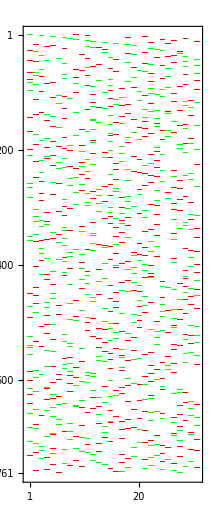

```mathematica
MatrixPlot[season,ColorRules->{0->White,1->Green,-1->Red}, MaxPlotPoints->Infinity]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["nbacurrentseason.mx",{season, delta,encode,decode}]
```